```mathematica
P=x px;
S=y (px/in);
P/(160A)S==(x/160 y)dp
```

(px^2 x y)/(160 A in)==(dp x y)/160

```mathematica
Solve[%,A]
```

{{A→px^2/(dp in)}}

```mathematica
(a(px/in)*b px)/(160 px^2 dp^-1 in^-1)//Simplify
```

(a b dp)/160

```mathematica
P
```

px x

```mathematica
Clear["`*"]
```

```mathematica
D
```

D

```mathematica
Solve[{D==(S S I0)/C1},D]
```

{{D→(I0 S^2)/C1}}

```mathematica
C1=160 px^2 dp^-1 in^-1
Solve[20dp==(I0 S^2)/C1,I0]
```

(160 px^2)/(dp in)

{{I0→(3200 px^2)/(in S^2)}}

```mathematica
I0/.%[[1,1]]
```

(3200 px^2)/(in S^2)

```mathematica
%/.S->ppi (px /in)
```

(3200 in)/ppi^2

```mathematica
%/in
```

3200/ppi^2

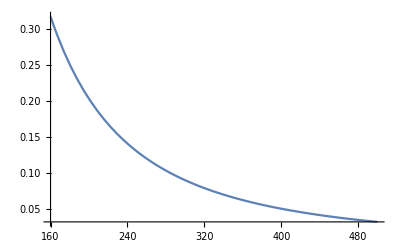

```mathematica
Plot[3200/ppi^2*2.54,{ppi,160,500}]
```